```mathematica
SetDirectory["/home/s1220054/Dissertation/Dissertation/DiSamp/src"]
```

/home/s1220054/Dissertation/Dissertation/DiSamp/src

```mathematica
data = Import["phidist.txt","CSV"]
```

{{24.0832,0.5},{13.0384,0.4},{63.5059,0.428571},{72.9452,0.5},{25.4951,0.238095},{46.6905,0.272727},26792,{81.3449,0.539498},{71.8471,0.539496},{68.2495,0.539494},{24.1868,0.539482},{102.005,0.539491},{6.32456,0.5395}}
 |  |  |  |

```mathematica
Transpose[data]
```

1
 |  |  |  |

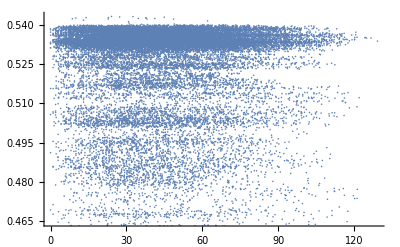

```mathematica
ListPlot[data]
```

```mathematica
data2 = Import["new.txt","CSV"]
```

{{259,296},{259,305},{259,306},{259,307},{259,308},{259,311},{259,316},{259,317},{260,292},{260,293},{260,294},{260,295},{260,296},4772,{338,310},{339,289},{339,298},{339,306},{339,307},{339,308},{339,309},{339,310},{340,301},{340,306},{340,307},{341,306}}
 |  |  |  |

```mathematica
data3 = Import["type2.txt","CSV"]
```

{{260,297},{261,297},{261,298},{262,291},{262,297},{262,314},{263,295},{263,297},{264,291},{264,300},{264,304},{264,305},{264,315},2713,{342,293},{342,295},{342,296},{342,297},{342,298},{342,299},{342,300},{342,304},{342,305},{343,296},{343,298},{343,299}}
 |  |  |  |

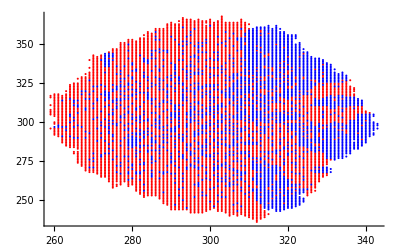

```mathematica
ListPlot[{data2,data3},PlotStyle->{Red,Blue}]
```